# Лабораторная работа №5

## Математические модели с запаздыванием

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
апрель 2022
ММФ, КМ и СА, доц. Лаврова О.А., доц. Щеглова Н.Л.
выполнил студент 
3 курса 5 группы ММФ БГУ
Кирилло Д.Е.

## Задание 1. Метод последовательного интегрирования (метод шагов)

Напишите пользовательскую функцию solveDelay[f_, T_, {t0_, tend_}, phi_], которая реализует метод последовательного интегрирования (метод шагов) для численного решения начальной задачи для одного дифференциального уравнения с запаздывающим аргументом

x'(t)==f(t,x(t),x(t-T)),      t_0<t≤t_end
x(t)==ϕ(t),                                         t_0-T≤t≤t_0

где T=const>0 определяет величину запаздывания, начальная функция ϕ(t) полагается заданной на начальном множестве I_0:=[t_0-T,t_0].

### Рекомендации по реализации Задания 1

Используйте функцию NDSolve для решения задачи Коши для обыкновенного дифференциального уравнения без запаздывания на каждом шаге метода.

Реализация последовательности шагов возможна с помощью оператора повторных действий NestList и функции Piecewise для представления кусочной гладкой функции решения на интервалах I_k:=[t_0+(k-1)T,t_0+k T].

```mathematica
?Piecewise
```

```mathematica
ClearAll[solveDelay];
solveDelay[f_,T_,{t0_,tend_},phi_]:=Piecewise[(* #⟦1⟧:=phi, #⟦2⟧:=t0*)
{#⟦1⟧[t],#⟦2⟧-T<t≤#⟦2⟧}&/@
Rest@NestList[
{NDSolve[{x'[t]==f[t,x[t],#⟦1⟧[t-T]],
x[#⟦2⟧]==#⟦1⟧[#⟦2⟧]},
x,
{t,#⟦2⟧,#⟦2⟧+T}]⟦1,1,2⟧,
#⟦2⟧+T}&, (*function*)
{phi,t0},(*expression*)
Ceiling[(tend-t0)/T] (*n*)
]
];
```

Пример, как строится функция solveDelay и его отображение на графике

```mathematica
solveDelay[Function[{x},Sin[x]],2,{0,7},Cos[(3π)/2#]&]
```

Piecewise[{{InterpolatingFunction[…][t], 0<t≤2}, {InterpolatingFunction[…][t], 2<t≤4}, {InterpolatingFunction[…][t], 4<t≤6}, {InterpolatingFunction[…][t], 6<t≤8}, {0, True}}]

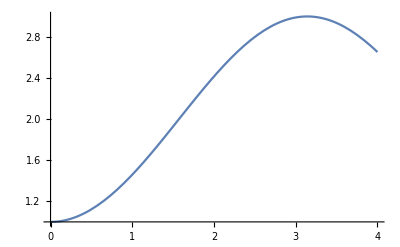

```mathematica
Plot[Evaluate[solveDelay[Function[{x},Sin[x]],2,{0,7},Cos[(3π)/2#]&]],{t,0,4}]
```

## Задание 2. Линейное дифференциальное уравнение уравнение с запаздывающим аргументом

Рассмотрим линейное дифференциальное уравнение с запаздывающим аргументом вида

x'(t)==-(π x(t-T))/(2 T).

### Задание 2.1 (Аналитическое решение)

Покажите с помощью символьных преобразований, что функция x(t)=C cos((π t)/(2 T)) является решением уравнения (2) для произвольного значения константы C и заданного значения параметра запаздывания T=const>0.

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
```

D:\ММДС

```mathematica
Import["LR5T2.1.pdf",{"PageImages",1}]
```

-Graphics-

### Задание 2.2 (Численное решение)

Сформулируйте произвольную начальную задачу для уравнения с запаздывающим аргументом (2). 

Решите численно сформулированную начальную задачу с помощью пользовательской функции solveDelay из Задания 1 и с помощью встроенной функции NDSolve. Сравните два численных решения графически и численно.

Рассмотрим начальную задачу для одного линейного дифференциального уравнения с запаздывающим аргументом

x'(t)== -sin(x(t-1)),      1≤t≤3,
x(t)==ϕ(t)=2t,                                         0<t≤1

где T=1>0 определяет величину запаздывания, которая уже учтена на отрезке, начальная функция ϕ(t) полагается заданной на начальном множестве I_0:=[t_0-T,t_0].

```mathematica
NDsol=NDSolve[{x'[t]==-Sin[x[t-1]],x[t/;t≤1]==2t},x,{t,1,5}]⟦1,1,2⟧
SDsol=solveDelay[-Sin[#3]&,1,{1,5},2#&]
```

InterpolatingFunction[…]

Piecewise[{{InterpolatingFunction[…][t], 1<t≤2}, {InterpolatingFunction[…][t], 2<t≤3}, {InterpolatingFunction[…][t], 3<t≤4}, {InterpolatingFunction[…][t], 4<t≤5}, {0, True}}]

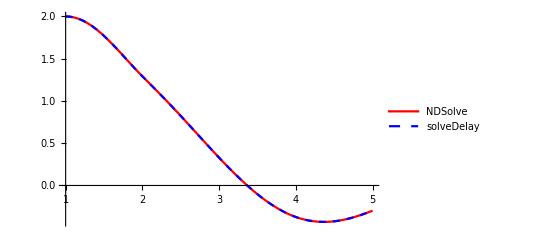

```mathematica
Plot[{NDsol[t],SDsol},{t,1,5},PlotStyle->{{Red},{Dashed,Blue}},PlotLegends->{"NDSolve","solveDelay"}]
```

Как видно из вышеприведенного графика, значения функции solveDelay и встроенной функции NDSolve совпадают между.

```mathematica
NDsol[#]&/@Range[2,5]
SDsol/.{t->#}&/@Range[2,5]
%==%% (*здесь может присутствовать несогласованность с числами с плавающей точкой, итоговые значения верны между собой*)
```

{1.29193,0.328617,-0.373027,-0.297911}

{1.29193,0.328617,-0.373027,-0.297911}

False

Как видно из полученных численных решений, значения функции solveDelay и встроенной функции NDSolve совпадают между.

## Задание 3. Начальная задача для уравнения Хатчинсона

### Математическая модель

Рассмотрим начальную задачу для уравнения Хатчинсона в безразмерных переменных

N'(t)==N(t)(1-N(t-T)),                 t>0
N(t)==ϕ(t),                                      -T≤t≤0

где начальная функция ϕ(t)=1+t/T задана на начальном множестве I_0=[-T,0], параметр запаздывания T=const>0.

### Задание 3.1 (Численное решение)

Изобразите в одной системе координат графики решений N(t) модели Хатчинсона (3), построенные с помощью пользовательской функции solveDelay из Задания 1 для различных значений T. Рассмотрите случаи  0<T<π/2, T=π/2, T>π/2.

0<T<π/2,где T=π/4

```mathematica
T=π/4;
SDsol1= solveDelay[#2(1-#3)&,T,{0,50},(1+#/T)&];
```

T=π/2.

```mathematica
T=π/2;
SDsol2= solveDelay[#2(1-#3)&,T,{0,50},(1+#/T)&];
```

T>π/2,где T=π

```mathematica
T=π;
SDsol3= solveDelay[#2(1-#3)&,T,{0,50},(1+#/T)&];
```

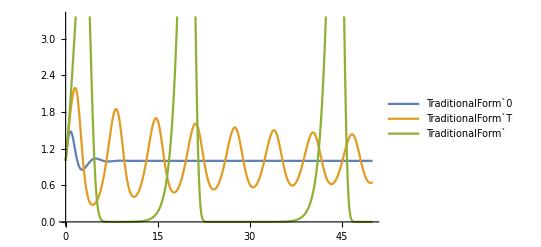

```mathematica
Plot[{SDsol1,SDsol2,SDsol3},{t,0,50},PlotLegends->{"TraditionalForm`0","TraditionalForm`T","TraditionalForm`"}]
```

Проверьте корректность построенных численных решений сравнением с решениями модели Хатчинсона (3), полученными с помощью NDSolve.

0<T<π/2,где T=π/4

```mathematica
T=π/4;
NDsol1=NDSolve[{NN'[t]==NN[t](1-NN[t-T]),NN[t/;t≤0]==1+t/T},NN,{t,0,50}]⟦1,1,2⟧
```

InterpolatingFunction[…]

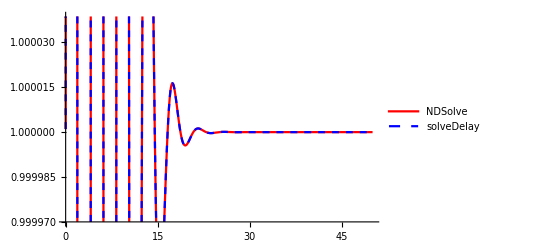

```mathematica
Plot[{NDsol1[t],SDsol1},{t,0,50},PlotStyle->{{Red},{Dashed,Blue}},PlotLegends->{"NDSolve","solveDelay"}]
```

T=π/2.

```mathematica
T=π/2;
NDsol2= NDSolve[{NN'[t]==NN[t](1-NN[t-T]),NN[t/;t≤0]==1+t/T},NN,{t,0,50}]⟦1,1,2⟧
```

InterpolatingFunction[…]

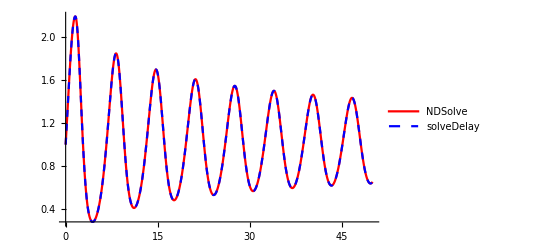

```mathematica
Plot[{NDsol2[t],SDsol2},{t,0,50},PlotStyle->{{Red},{Dashed,Blue}},PlotLegends->{"NDSolve","solveDelay"}]
```

Как можно заметить из вышеприведенного графика, при T=π/2 наблюдаются колебательные движения. Причем данное движение будет затухающим при t->∞.

T>π/2,где T=π

```mathematica
T=π;
NDsol3= NDSolve[{NN'[t]==NN[t](1-NN[t-T]),NN[t/;t≤0]==1+t/T},NN,{t,0,50}]⟦1,1,2⟧
```

InterpolatingFunction[…]

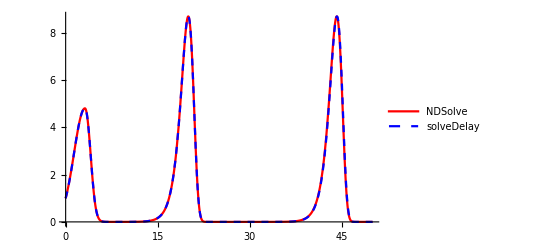

```mathematica
Plot[{NDsol3[t],SDsol3},{t,0,50},PlotStyle->{{Red},{Dashed,Blue}},PlotLegends->{"NDSolve","solveDelay"}]
```

Как видно из вышеприведенных графиков, значения функции solveDelay и встроенной функции NDSolve совпадают между.

### Задание 3.2 (Качественное поведение)

На основании построенных графиков решений в Задании 3.1 сформулируйте выводы о характере устойчивости положения равновесия N(t)≡1 модели Хатчинсона (3) для случаев 0<T<π/2, T=π/2, T>π/2.

```mathematica
Import["LR5T3.2.pdf",{"PageImages",1}]
```

-Graphics-

## Задание 4. Модель регуляции концентрации клеток крови

### Математическая модель

c'(t)==(λ a^m c(t-T))/(a^m+(c(t-T))^m)-g c(t),    t>0
c(t)==ϕ(t),                                         -T≤t≤0

где c(t)≥0 -- концентрация клеток крови, T=const>0 -- временная задержка в воспроизводстве новых клеток крови и поступлении их в кровоток,  λ=const>0, a=const>0, m=const>0, g=const>0 -- заданные параметры модели.  Первое слагаемое в правой части уравнения отвечает за воспроизводство клеток, второе слагаемое -- за гибель клеток.

При обезразмеривании концентрации вида c^*=c/a уравнение модели (4) запишется в виде

(ⅆc^*(t))/ⅆt==(λ c^*(t-T))/(1+(c^*(t-T))^m)-g c^*(t).

Математическая модель (4) впервые предложена в [3].

### Задание 4.1 (Численное решение)

Решите численно начальную задачу для уравнения (5) с помощью пользовательской функции solveDelay для следующих значений параметров, соответствующих процессу регуляции лейкоцитов,

(a) λ=0.2 день^-1, m=10, g=0.1 день^-1, T=6  дней,
(b) λ=0.2 день^-1, m=10, g=0.1 день^-1, T=20  дней

и для начальной функции ϕ(t)=0.1, заданной на начальном множестве I_0=[-T,0] , при 0≤ t≤600 дней.

Анализируя уравнение (5), покажите, что одним из положений равновесия для параметров (a) и (b) является решение вида c^*(t)≡1.

Сравните построенные численные решение с приведенными ниже решениями из [1, стр. 27, Рис. 1.15] для случаев (а) и (b), соответственно.

Случай (a) λ=0.2 день^-1, m=10, g=0.1 день^-1, T=6  дней и ϕ(t)=0.1, заданной на начальном множестве I_0=[-T,0] , при 0≤ t≤600 дней.

```mathematica
λ=0.2;m=10;g=0.1;tEnd=600;ϕ=0.1;T=6; 
SDsol4= solveDelay[(λ #3)/(1+#3^m)-g#2&,T,{0,tEnd},ϕ&];
```

Случай (b) λ=0.2 день^-1, m=10, g=0.1 день^-1, T=20 дней и ϕ(t)=0.1, заданной на начальном множестве I_0=[-T,0] , при 0≤ t≤600 дней.

```mathematica
λ=0.2;m=10;g=0.1;tEnd=600;ϕ=0.1;T=20; 
SDsol5= solveDelay[(λ #3)/(1+#3^m)-g#2&,T,{0,tEnd},ϕ&];
```

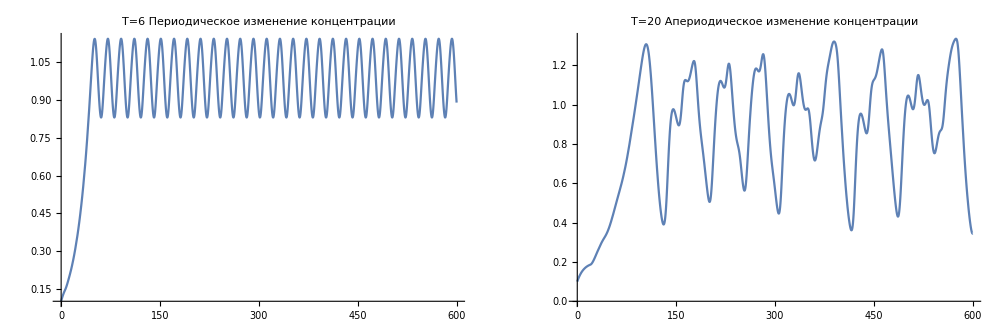

-Graphics-

```mathematica
GraphicsRow[{Plot[SDsol4,{t,0,tEnd},PlotRange->Full,PlotLabel->"Т=6\n Периодическое изменение концентрации"],Plot[SDsol5,{t,0,tEnd},PlotLabel->"Т=20\n Aпериодическое изменение концентрации"]},ImageSize->1000]
```

Сравнив графики, приведенные из книги и которые получили входе построения через функцию solveDelay, можно сделать вывод о том, что графики  между собой совпадают, значит функция solveDelay была построена верно.
По графикам численных решений видно, что величина запаздывания T в воспроизводстве лейкоцитов влияет на динамику изменения концентрации: периодическое или апериодическое поведение. 
Шестидневный период (T=6) является нормой для изменения концентрации лейкоцитов в крови человека. Увеличение периода приводит к апериодическому изменению концентрации и может являться причиной нарушений здоровья и заболеваний человека.  Соответственно, при Т=6 мы получаем периодическое изменение концентрации, а при Т=20 у нас выходит апериодическое изменение концентрации, что явно показано на графиках выше.
Покажем, что положение равновесия для параметров (a) и (b) является решение вида c^*(t)≡1.
Так как, по заданным нашим данным, параметры  для случая (a) и (б), а именно λ=0.2 день^-1, m=10, g=0.1 день^-1,  и ϕ(t)=0.1, заданной на начальном множестве I_0=[-T,0] , при 0≤ t≤600 дней, равны между собой, исключение составляет только переменная продолжительности периода Т, но, по условию, c^*(t)≡1, то данное значение никак не повлияет на наш конечный результат. Учитывая все приведенные факторы, а также, что дифференциал от c^*(t)≡1 равна 0, мы получаем, что
0==0.2/(1+1^10)-0.1 ;
0=0.1-0.1;
0=0. 
То есть мы пришли к выводу о том, что для параметров (a) и (b)  решение вида c^*(t)≡1 является положением равновесия.

### Задание 4.2 (Фазовый портрет)

Качественное поведение решения для рассматриваемой модели регуляции концентрации клеток крови (периодическое поведение или апериодическое поведение) можно определить по траекториям в фазовой плоскости (c(t),c(t-T)).

λ=2, g=1, T=2 ,m={7,7.75, 8.5, 8.79,9.65, 9.69715, 9.6975, 9.76, 10, 20}. Начальная функцию ϕ(t)=0.9 на начальном множестве I_0=[-T,0]  .

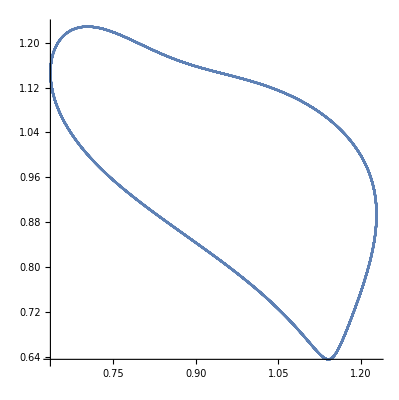
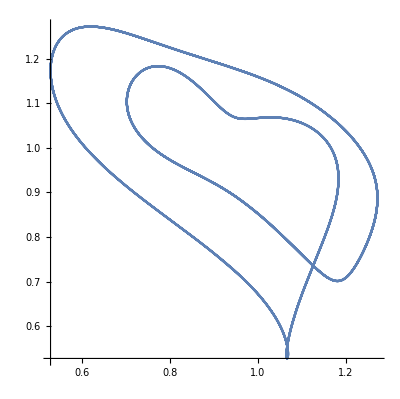
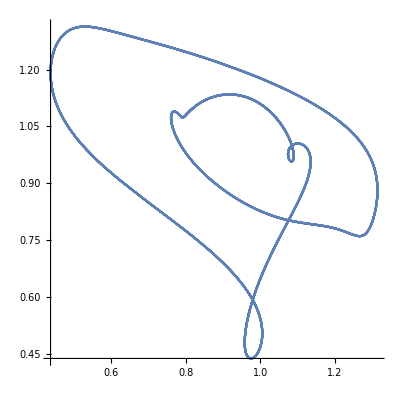
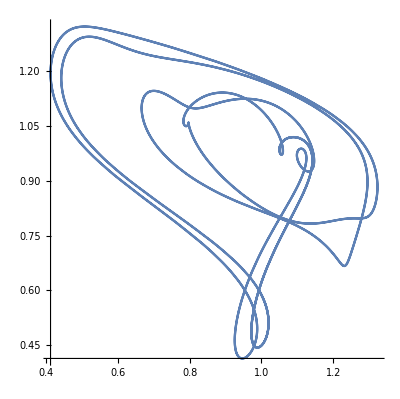
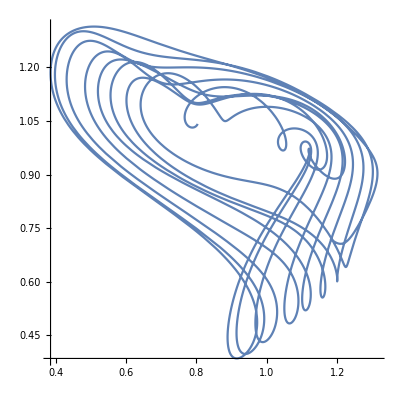
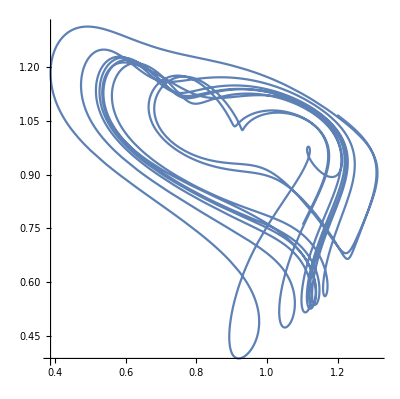
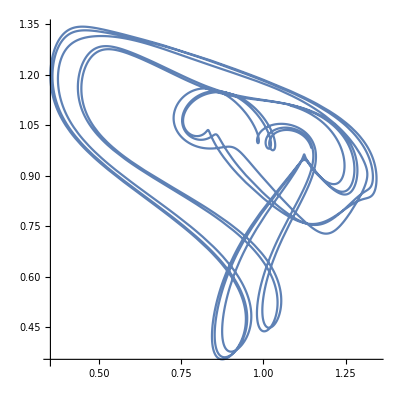
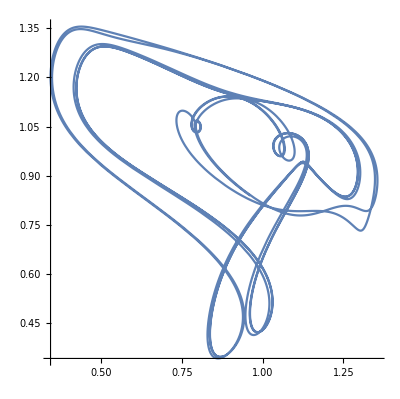

```mathematica
λ=2;g=1;tEnd=600;ϕ=0.9;T=2;m ={7,7.75,8.5,8.79,9.65,9.69715,9.6975,9.76,10,20};
ClearAll[SolveDelay];
SolveDelay[m_]:=((λ #3)/(1+#3^m)-g#2)&;
ParametricPlot[{#/.t->t1,#/.t->t1-T},{t1,300,350}]&[solveDelay[SolveDelay[#],T,{0, tEnd},ϕ&]]&/@m
```

Изобразите фазовые траектории решений начальной задачи для уравнения (5) при фиксированных значениях параметров λ=2, g=1, T=2 и различных значениях параметра m={7,7.75, 8.5, 8.79,9.65, 9.69715, 9.6975, 9.76, 10, 20}. Начальная функцию ϕ(t)=0.9 на начальном множестве I_0=[-T,0]  .

Сравните с аналогичными фазовыми траекториями численных решений из [1, стр. 29, Рис. 1.16] и [3, Рис. 6].

-Graphics-

На основании построенных фазовых траекторий сформулируйте выводы о качественном поведении решения математической модели для уравнения (5) в окрестности положения равновесия  c(t)≡1 для различных значений параметра m.

Сравнив фазовые траектории из книги и которые получили входе построения через ParametricPlot, можно сделать вывод о том, что графики между собой совпадают, единственным минусом является то, что иногда трудно определить само значение продолжительности времени моделирования, то есть tEnd.
Как можно заметить из получившихся графиков,  чем больше значение m, тем более появляются нестандартные  движения поведения нашей модели, однако, пройдя некоторые определенные шаги, наша модель возвращается к изначальным своим траекториям, чтобы опять начать нестандартные фазовые траектории.
Стоит отметить, что даже небольшие относительные изменения значения m ведет за собой более нестандартное построение фазовых траекторий модели при t->∞.

## Литература

[1] Д. Мюррей. Математическая биология. Том I. Введение. -- М.-Ижевск, 2009.

[2] Л. Э. Эльсгольц, С. Б. Норкин. Введение в теорию дифференциальных уравнений с отклоняющимся аргументом. -- М.: Наука, 1971.

[3] L. Glass, M. C. Mackey. Pathological conditions resulting from instabilities in physiological control systems. Ann. N. Y. Acad. Sci., 316:214--235, 1979.

[4] А. Д. Мышкис. Линейные дифференциальные уравнения с запаздывающим аргументом. -- М.: Наука, 1972.

[5] Ю. Ф. Долгий, П. Г. Сурков. Математические модели динамических систем с запаздыванием. -- Екатеринбург: Изд-во Урал. ун-та, 2012.